```mathematica
years = {1902,1907,1912,1917}; population = {1174700,1345700,1617157,1854400}
```

{1174700,1345700,1617157,1854400}

```mathematica
x = Map[Function[xi, xi-1900], years]; y = Map[ Function[yi, yi/ 1000000], population]
```

{11747/10000,13457/10000,1617157/1000000,1159/625}

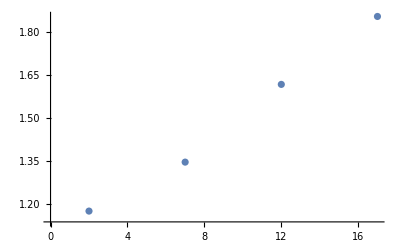

```mathematica
ListPlot[Table[{x[[i]], y[[i]]},{i,4}]]
```

```mathematica
F[a_,b_,c_,d_]:=Sum[(yi-a xi^3-b xi^2-c xi-d)^2, {i, 4}]
```

```mathematica
Print[D[F[a,b,c,d],a]==0];
Print[D[F[a,b,c,d],b]==0];
Print[D[F[a,b,c,d],c]==0];
Print[D[F[a,b,c,d],d]==0]
```

-8 xi^3 (-d-c xi-b xi^2-a xi^3+yi)==0

-8 xi^2 (-d-c xi-b xi^2-a xi^3+yi)==0

-8 xi (-d-c xi-b xi^2-a xi^3+yi)==0

-8 (-d-c xi-b xi^2-a xi^3+yi)==0

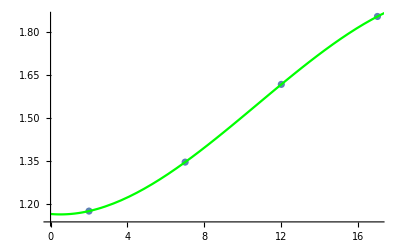

```mathematica
Show[ListPlot[Table[{x[[i]], y[[i]]},{i,4}]],Plot[-0.00017956133333323724 t^3 +0.005779927999997216 t^2-0.005788742666644684t+1.1645942639999614,{t,0,20}, PlotStyle->{Green}]]
```

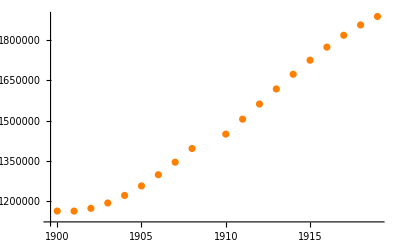

```mathematica
lagrangeList = {1164594.2640000002,1164405.888,1174700,1194399.232,1222426.216,1257703.5840000003,1299153.9679999999,1345700,1396264.3119999997,1449769.5359999998,1505138.304,1561293.2480000001,1617157,1671652.192,1723701.4560000002,1772227.4239999999,1816152.7280000006,1854400,1885891.8719999997,1909550.9759999993};
yearsList = {1900, 1901, 1902, 1903, 1904, 1905, 1906, 1907,1908, 1910,1911, 1912, 1913, 1914, 1915, 1916, 1917, 1918,1919};
ListPlot[Table[{yearsList[[i]], lagrangeList[[i]]},{i,19}],PlotStyle->{Orange}]
```

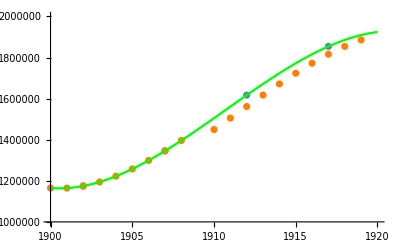

```mathematica
Show[ListPlot[Table[{years[[i]], population[[i]]},{i,4}], PlotRange->{{1900, 1920},{1000000,2000000}}],ListPlot[Table[{yearsList[[i]], lagrangeList[[i]]},{i,19}], PlotStyle->{Orange},PlotRange->{{1900, 1920},{1000000,2000000}}],Plot[(-0.00017956133333323724 (t-1900)^3 +0.005779927999997216 (t-1900)^2-0.005788742666644684(t-1900)+1.1645942639999614)*1000000,{t,1900,1920}, PlotStyle->{Green},PlotRange->{{1900, 1920},{1000000,2000000}}]]
```